This document is long enough that it is annoying to have all the sections open at once.

CDF users: look through the menu items to find out how to expand sections. Alternatively, the shortcut should be Ctrl+‘
Mathematica users: I recommend enabling “Preferences>Interface>Show open/close icon for cell groups” to help with section management.

### Init

Global rules for simplification:

```mathematica
$Assumptions=0<β<γ<α&&0≤p≤1&&x≥0&&y≥0&&z≥0;
```

Macro for exporting figures to file:

```mathematica
$doExport=False;
exportme[name_,opt:OptionsPattern[Export]][fig_]:=(SetDirectory[NotebookDirectory[]];
If[$doExport,
Export["../fig/"<>name<>".pdf",fig,opt];Export["../fig/"<>name<>".png",fig,opt]];fig)
```

### Hyper-Prior

Functions to generate priors of the hyper parameters. The first is normal, the second is bivariate Poisson.

```mathematica
hyperPriorNormal[αbar_,βbar_,αsigma_,βsigma_,αβsigma_]:=MultinormalDistribution[{αbar,βbar},{{αsigma^2,αβsigma},{αβsigma,βsigma^2}}]
```

```mathematica
hyperPriorBP[αbar_,βbar_,αsigma_,βsigma_,αβsigma_]:=Module[{θ0,θ1,θ2},TransformedDistribution[{θ1+θ0,θ2+θ0},{
θ0\[Distributed]GammaDistribution[αβsigma,1],
θ1\[Distributed]GammaDistribution[(αbar-αβsigma)^2/(αsigma^2-αβsigma),((αbar-αβsigma)/(αsigma^2-αβsigma))^-1],
θ2\[Distributed]GammaDistribution[(βbar-αβsigma)^2/(βsigma^2-αβsigma),((βbar-αβsigma)/(βsigma^2-αβsigma))^-1]
}]];
```

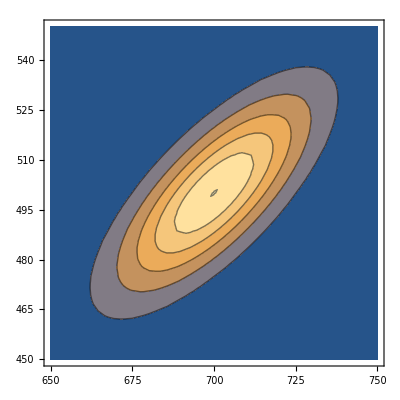
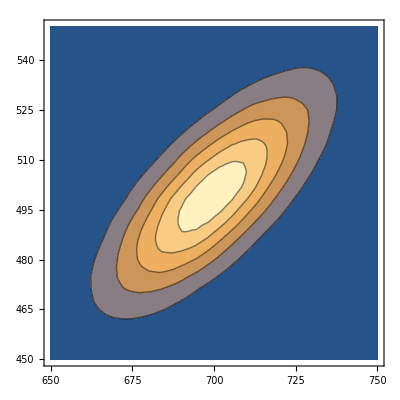

```mathematica
With[{bp=PDF[SmoothKernelDistribution@RandomVariate[hyperPriorBP[700.,500.,20.,20.,300.],500000],{α,β}]},
Row[{
ContourPlot[PDF[hyperPriorNormal[700,500,20,20,300],{α,β}],{α,650,750},{β,450,550},PlotRange->All,ImageSize->400],
ContourPlot[bp,{α,650,750},{β,450,550},PlotRange->All,ImageSize->400]
}]
]
```

### Model

Our model is just three (conditionally-) independent Poisson draws for bright, dark, and signal counts. We call draws from each x,y, and z respectively.

```mathematica
model[α_,β_,p_]:=ProductDistribution[PoissonDistribution[α],PoissonDistribution[β],PoissonDistribution[β+(α-β)p]]
```

```mathematica
likelihood[α_,β_,p_,x_,y_,z_]=PDF[model[α,β,p],{x,y,z}]//Simplify
```

(ⅇ^(-(1+p) α+(-2+p) β) α^x β^y (p (α-β)+β)^z)/(x! y! z!)

We do get correct listability list of data

```mathematica
likelihood[α,β,p,{x1,x2},{y1,y2},{z1,z2}]
likelihood[7000,5000,0.5,{7050,6049},{5000,4950},{6000,6500}]
```

{(ⅇ^(-(1+p) α+(-2+p) β) α^x1 β^y1 (p (α-β)+β)^z1)/(x1! y1! z1!),(ⅇ^(-(1+p) α+(-2+p) β) α^x2 β^y2 (p (α-β)+β)^z2)/(x2! y2! z2!)}

{1.1552820199×10^-7,6.6483251319×10^-46}

Also make a pattern for only z data:

```mathematica
likelihood[α_,β_,p_,z_]=Exp[-p α+(-1+p) β+z Log[p (α-β)+β]-Log[z!]];(*(ⅇ^(-p (α-β)-β) (p (α-β)+β)^z)/(z!);*)
```

It is worthwhile to compile the likelihood in this last case for the Bayesian estimator. Note that Factorial is not a compileable function, so we implement it manually.We don’t even try to make it efficient. We work in logarithmic space to reduce numerical error.

```mathematica
likelihoodC=Compile[{{α,_Real,1},{β,_Real,1},{p,_Real,1},{z,_Integer}},
Exp[-p α+(-1+p) β+z Log[p (α-β)+β]-Plus@@Log[Range[z]]]
];
likelihoodCC=Compile[{{α,_Real,1},{β,_Real,1},{p,_Real,1},{z,_Integer}},
Exp[-p α+(-1+p) β+z Log[p (α-β)+β]-Plus@@Log[Range[z]]],
CompilationTarget->"C"
];
```

We also try a faster implementation of log-factorial, found at http://www.johndcook.com/blog/2010/08/16/how-to-compute-log-factorial/
We also improve numerical stability by subtracting the max log-likelihood before exponentiating; this does not provide the correct probabilities (as seen in the accuracy table below) but it does if you subsequently normalize a list of probabilities, as is done is estimatorBayes.

```mathematica
logfaclookup=N@Table[Log@Factorial[n],{n,0,256}];
likelihoodCa=With[{lookup=logfaclookup},Compile[{{α,_Real,1},{β,_Real,1},{p,_Real,1},{z,_Integer}},
Exp[#-Max[#]]&[-p α+(-1+p) β+z Log[p (α-β)+β]-If[z≤256,lookup[[z+1]],(z+0.5)Log[z+1]-z-1+0.5 Log[2 π]+1/(12z+12)]]
]];
loglikelihoodCa=With[{lookup=logfaclookup},Compile[{{α,_Real,1},{β,_Real,1},{p,_Real,1},{z,_Integer}},
-p α+(-1+p) β+z Log[p (α-β)+β]-If[z≤256,lookup[[z+1]],(z+0.5)Log[z+1]-z-1+0.5 Log[2 π]+1/(12z+12)]
]];
likelihoodCCa=With[{lookup=logfaclookup},Compile[{{α,_Real,1},{β,_Real,1},{p,_Real,1},{z,_Integer}},
Exp[#-Max[#]]&[-p α+(-1+p) β+z Log[p (α-β)+β]-If[z≤256,lookup[[z+1]],(z+0.5)Log[z+1]-z-1+0.5 Log[2 π]+1/(12z+12)]],
CompilationTarget->"C"
]];
loglikelihoodCCa=With[{lookup=logfaclookup},Compile[{{α,_Real,1},{β,_Real,1},{p,_Real,1},{z,_Integer}},
-p α+(-1+p) β+z Log[p (α-β)+β]-If[z≤256,lookup[[z+1]],(z+0.5)Log[z+1]-z-1+0.5 Log[2 π]+1/(12z+12)],
CompilationTarget->"C"
]];
```

Whether the compiled-C or compiled does better seems to depend on the amount of data. In either case, a huge improvement over the usual evaluation for lots of data.

```mathematica
Module[{testVals=RandomVariate[hyperPriorBP[70000,50000,200,200,80],100000],l,lc,lcc,lca,lcca},
testVals=Join[testValsᵀ,{ConstantArray[0.5,Length@testVals]}]ᵀ;
(l=likelihood[testVals[[All,1]],testVals[[All,2]],testVals[[All,3]],60000];//Timing//First//Print);
(lc=likelihoodC[testVals[[All,1]],testVals[[All,2]],testVals[[All,3]],60000];//Timing//First//Print);
(lcc=likelihoodCC[testVals[[All,1]],testVals[[All,2]],testVals[[All,3]],60000];//Timing//First//Print);
(lca=likelihoodCa[testVals[[All,1]],testVals[[All,2]],testVals[[All,3]],60000];//Timing//First//Print);
(lcca=likelihoodCCa[testVals[[All,1]],testVals[[All,2]],testVals[[All,3]],60000];//Timing//First//Print);
Outer[Max[Abs[#1-#2]]&,{l,lc,lcc,lca,lcca},{l,lc,lcc,lca,lcca},1]//MatrixForm
]
```

0.132

0.008

0.008

0.004

0.008

(0. | 1.39939×10^-12 | 1.39939×10^-12 | 0.998371 | 0.998371
1.39939×10^-12 | 0. | 0. | 0.998371 | 0.998371
1.39939×10^-12 | 0. | 0. | 0.998371 | 0.998371
0.998371 | 0.998371 | 0.998371 | 0. | 0.
0.998371 | 0.998371 | 0.998371 | 0. | 0.)

### Data-Generator

Draws nParams from the hyper prior to get references, and uses each reference along with p to draw samples from the model

```mathematica
genData[p_,hyperPrior_,nParam_,nSampPerParam_]:=Module[{params,data},
params=RandomVariate[hyperPrior,nParam];
data=Table[{{Sequence@@param,p},RandomVariate[model[Sequence@@param,p],nSampPerParam]},{param,params}];
data
]
```

Test:

```mathematica
genData[0.5,hyperPriorNormal[700,500,200,200,80],5,2]
```

{{{647.891,534.354,0.5},{{651,538,595},{683,530,572}}},{{322.734,441.624,0.5},{{351,459,375},{313,437,393}}},{{859.866,119.072,0.5},{{893,118,496},{795,128,483}}},{{723.917,731.481,0.5},{{780,723,757},{726,730,725}}},{{656.409,558.95,0.5},{{668,571,622},{678,557,609}}}}

Extreme example of αs being a mixture distribution because of large αsigma in hyperPrior:

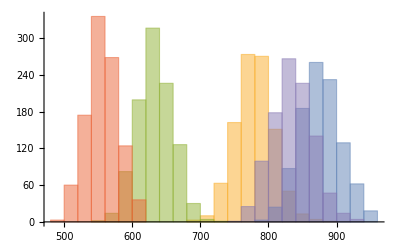

```mathematica
Histogram[genData[0.5,hyperPriorNormal[700,500,200,200,80],5,1000][[All,2,All,1]]]
```

### MLE

MLE of the model. We are actually using the biased estimator with ϵ=0.01 to avoid dividing by zero.

```mathematica
estimatorMLE[data_]:=(data[[3]]-data[[2]])/(data[[1]]-data[[2]]+0.01)
```

```mathematica
estimatorMLE[Last[#]ᵀ]&/@genData[0.5,hyperPriorBP[70000,50000,200,200,80],5,10]
```

{{0.522518,0.499301,0.513973,0.511832,0.482278,0.49954,0.516148,0.483618,0.504562,0.481679},{0.504488,0.499537,0.532479,0.499023,0.518454,0.508779,0.481837,0.483492,0.493179,0.483253},{0.499119,0.494731,0.481234,0.50186,0.492909,0.51775,0.484432,0.512543,0.512239,0.499197},{0.513758,0.502655,0.501192,0.521791,0.51734,0.507617,0.485817,0.496383,0.488377,0.481777},{0.493351,0.487193,0.48013,0.497646,0.512001,0.482738,0.507404,0.489878,0.525161,0.52794}}

### MLE Bias Corrected

Try the bias corrected MLE:

```mathematica
estimatorMLEBC[data_]:=With[{x=data[[1]],y=data[[2]],z=data[[3]]},
(z((x-y)^2-x-y)-y((x-y)^2-2x-2y))/((x-y)^3+0.01)
]
```

```mathematica
estimatorMLEBC[Last[#]ᵀ]&/@genData[0.5,hyperPriorBP[70000,50000,200,200,80],5,10]
```

{{0.487808,0.52324,0.515004,0.532936,0.500377,0.516347,0.49546,0.493176,0.506131,0.486716},{0.525416,0.529497,0.518835,0.478985,0.501725,0.522374,0.503905,0.494116,0.49979,0.482844},{0.502693,0.494671,0.515034,0.504083,0.54797,0.507824,0.497415,0.498849,0.509404,0.512953},{0.483107,0.518306,0.495812,0.487544,0.495288,0.528062,0.505714,0.506815,0.495175,0.492838},{0.49138,0.501241,0.50754,0.508481,0.487635,0.505436,0.521419,0.508526,0.511251,0.495932}}

### Bayes

The Bayes estimator is quite a bit more work to set up. We do this over 4 subsections.

#### Priors

Put a uniform prior on p, and a product of Gammas (conjugate to product of Poisson) on α and β.

```mathematica
uniformP=UniformDistribution[];
```

```mathematica
uncorrRefPrior[μα_,μβ_,σα_,σβ_]:=ProductDistribution[GammaDistribution[(μα/σα)^2,(μα/σα^2)^-1],GammaDistribution[(μβ/σβ)^2,(μβ/σβ^2)^-1]]
```

The moments work as expected:

```mathematica
Mean[uncorrRefPrior[μα,μβ,σα,σβ]]
FullSimplify[StandardDeviation[uncorrRefPrior[μα,μβ,σα,σβ]],Assumptions->μα>0&&μβ>0&&σα>0&&σβ>0]
```

{μα,μβ}

{σα,σβ}

#### Uncorrelated Posterior

The posterior of product gamma distribution prior with respective mean/std (μα,σα) and (μβ,σβ)

```mathematica
({ap->a+x,bp->b+1}/.First@Solve[{μ==a/b,σ^2==a/b^2},{a,b}])//FullSimplify
{ap/bp,ap/bp^2}/.({ap->a+x,bp->b+1}/.First@Solve[{μ==a/b,σ^2==a/b^2},{a,b}])//FullSimplify
```

{ap→x+μ^2/σ^2,bp→1+μ/σ^2}

{(μ^2+x σ^2)/(μ+σ^2),(σ^2 (μ^2+x σ^2))/((μ+σ^2)^2)}

Return a function that computes the posterior given data tuple (x,y):

```mathematica
uncorrRefPosterior[μα_,μβ_,σα_,σβ_][x_,y_]:=ProductDistribution[GammaDistribution[x+(μα/σα)^2,(1+μα/σα^2)^-1],GammaDistribution[y+(μβ/σβ)^2,(1+μβ/σβ^2)^-1]]
```

Posterior sits on top of data point:

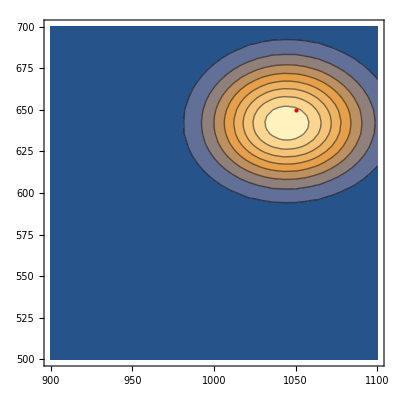

```mathematica
ContourPlot[PDF[uncorrRefPosterior[1000,600,100,60][1050,650],{α,β}],{α,900,1100},{β,500,700},Epilog->{Red,Point[{1050,650}]},PlotRange->All]
```

#### Correlated Posterior

Now we need to implement the bivariate Poisson posterior,  which is slightly non-trivial to get right just because there are so many indices and variable floating around. Mixture weights of the posterior.

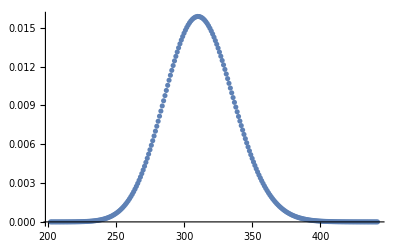

```mathematica
weightFcn[α0_,α1_,α2_,β1_,β2_,x_,y_,k_]=(LogGamma[α1-k+x]+LogGamma[α2-k+y]+LogGamma[α0+k]+
k Log[((1+β1)(1+β2))/2]-LogGamma[x-k+1.]-LogGamma[y-k+1.]-LogGamma[k+1.]);
posteriorWeights=Function[{μx,σx,μy,σy,σxy,x,y},
Module[{p,out,indeces,max,α1=-(μx-σxy)^2/(-σx^2+σxy)//N,α2=-(μy-σxy)^2/(σxy-σy^2)//N,α0=σxy//N,β1=(-μx+σxy)/(-σx^2+σxy)//N,β2=(-μy+σxy)/(σxy-σy^2)//N,const,wf},
const=α1 Log[β1]+α2 Log[β2]-LogGamma[α1]-LogGamma[α2]-LogGamma[α0];
wf=Function[{k},Re[Evaluate[const+weightFcn[α0,α1,α2,β1,β2,x,y,k]]]];
(*Evaluate wf a little bit at a time to avoid computing way more than we need to *)
p=Exp@Table[Evaluate[wf[k]],{k,0,200}];
(*Stop when adding 100 more points doesn't add up to at least 1% more weight*)
While[Length[p]-1<Min[x,y]&&Total[p[[-100;;]]]/Total[p]>0.01,
p=Join[p,Exp@Table[Evaluate[wf[k]],{k,Length[p],Min[x,y,Length[p]-1+100]}]]
];
p=Abs[p/Total[p]];
max=Max[p];
out=Transpose[{Range[0,Length[p]-1],p}];
out=Select[out,#[[2]]>max/10^5&]ᵀ;
{out[[1]],out[[2]]/Total[out[[2]]]}
]
];
ListPlot@Transpose@posteriorWeights[100000,500,60000,450,300,100500,65000]
```

```mathematica
posteriorWeights[1000,50,600,30,300,1050,650];//Timing
posteriorWeights[100000,500,60000,450,300,345344353,43534];//Timing
```

{0.008,Null}

{0.008,Null}

We don’t actually use the following definition because it is way too slow when all we want to do is draw random variates.

```mathematica
corrRefPosterior[μx_,σx_,μy_,σy_,σxy_][x_,y_?NumericQ]:=Module[{weights,indeces,θ1,θ2,θ3,α1,α2,α3,β1,β2},
{indeces,weights}=posteriorWeights[μx,σx,μy,σy,σxy,x,y];
α1=-N@((μx-σxy)^2/(-σx^2+σxy));α2=-N@((μy-σxy)^2/(σxy-σy^2));α3=N@σxy;β1=N@((-μx+σxy)/(-σx^2+σxy));β2=N@((-μy+σxy)/(σxy-σy^2));
TransformedDistribution[
{θ1+θ3,θ2+θ3},
{θ1,θ2,θ3}\[Distributed]MixtureDistribution[weights,
Table[ProductDistribution[
GammaDistribution[α1-k+x,(β1+1)^-1],
GammaDistribution[α2-k+y,(β2+1)^-1],
GammaDistribution[α3+k,(1+1)^-1]
],{k,indeces}]
]]
]
```

Instead we do the random sampling a bit more manually:

```mathematica
ClearAll@corrRefPosterior;
corrRefPosterior/:RandomVariate[corrRefPosterior[μx_,μy_,σx_,σy_,σxy_?NumericQ][x_,y_?NumericQ],n_?NumericQ]:=Module[{dist,weights,indeces,θ1,θ2,θ3,α1,α2,α3,β1,β2},
α1=-N@((μx-σxy)^2/(-σx^2+σxy));α2=-N@((μy-σxy)^2/(σxy-σy^2));α3=N@σxy;β1=N@((-μx+σxy)/(-σx^2+σxy));β2=N@((-μy+σxy)/(σxy-σy^2));
{indeces,weights}=posteriorWeights[μx,σx,μy,σy,σxy,x,y];
(*Figure out how many samples of each mixand we need*)
dist=Select[{indeces,RandomVariate[MultinomialDistribution[n,weights]]}ᵀ,Last[#]>0&];
(*Then draw the appropriate number of samples from each product distribution. Note that the order of this list is not randomized. *)
Join@@Map[With[{
a=RandomVariate[GammaDistribution[α1-#[[1]]+x,(β1+1)^-1],#[[2]]],
b=RandomVariate[GammaDistribution[α2-#[[1]]+y,(β2+1)^-1],#[[2]]],
c=RandomVariate[GammaDistribution[α3+#[[1]],(1+1)^-1],#[[2]]]
},{a+c,b+c}]ᵀ&,dist,1]
]
```

```mathematica
RandomVariate[corrRefPosterior[1000,600,50,30,500][1050,650],1000]//Dimensions//Timing
RandomVariate[corrRefPosterior[100000,2 Sqrt[100000],60000,2Sqrt[60000],1.5Sqrt[60000]][150000,65000],1000]//Dimensions//Timing
```

{0.04,{1000,2}}

{0.044,{1000,2}}

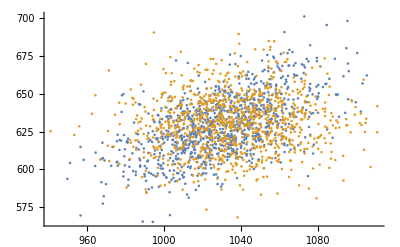

```mathematica
ListPlot[{RandomVariate[corrRefPosterior[1000,600,50,30,500][1050,650],1000],RandomVariate[uncorrRefPosterior[1000,600,50,30][1050,650],1000]}]
```

#### Estimators

We use a particle approximation for our estimator. This is simply because a closed form expression for the mean of the posterior is intractable, even when the reference posterior is known as a product of gammas, even when the prior for p is flat. Perhaps there is some better prior for p? I doubt it.

```mathematica
estimatorBayes[pprior_,refPosterior_,nParticles_:3000][data_]:=Module[{sigData,makeIntermediateParticles,particles,likelihoods},
(* Apoligies if this function is difficult to parse; it needed to work for arrays of data *)
(* Sample from the prior on p to get particles for the particles approximation *)
particles=RandomVariate[pprior,nParticles];
(* Since we know the posterior of the references, sample from this instead of using a particle update *)
makeIntermediateParticles[x_,y_]:=Join[RandomVariate[refPosterior[x,y],nParticles]ᵀ,{particles}]ᵀ;
particles=makeIntermediateParticles@@@(data[[{1,2}]]ᵀ);
(* Now compute the likelihoods of all particles given the z data *)
likelihoods=MapThread[likelihoodCCa[Sequence@@(#1ᵀ),#2]&,{particles,data[[3]]},1];
(* Finally, normalize the likelihoods and use them to approximate the mean of the posteriors *)
likelihoods=Map[(#/Total[#])&,likelihoods];
Map[Total,(likelihoods * particles[[All,All,3]]),{1}]
]
```

```mathematica
estimatorBayes[uniformP,uncorrRefPosterior[70000,50000,200,200],100][Transpose@Last@First@genData[0.5,hyperPriorBP[70000,50000,10,10,10],500,10]]
```

{0.484572,0.500048,0.500017,0.507047,0.505135,0.492377,0.508414,0.510103,0.491684,0.492003}

```mathematica
estimatorBayes[uniformP,corrRefPosterior[70000,50000,200,200,200],100][Transpose@Last@First@genData[0.65,hyperPriorBP[70000,50000,10,10,10],500,10]]
```

{0.621669,0.631279,0.62841,0.666748,0.641577,0.66872,0.616057,0.674927,0.637035,0.618098}

### Loss Functions

Define the mean squared error loss function:

```mathematica
mse[p_,pestimate_]:=Total[(p-pestimate)^2]/If[ListQ[pestimate],Length[pestimate],1]
```

```mathematica
Mean[mse[First[#1]⟦3⟧,estimatorMLE[Last[#]ᵀ]]&/@genData[0.5,hyperPriorNormal[7000,5000,2Sqrt[7000],2 Sqrt[3500],1.5 Sqrt[3500]],50,1000]]
```

0.00225328

### Risk Definition

```mathematica
monteCarloRisk[estimator_,loss_,pvals_,hyperPrior_,nParam_,nSampPerParam_]:=Module[{data,estimates},
Table[
data=genData[p,hyperPrior,nParam,nSampPerParam];
{p,Mean[loss[First[#]⟦3⟧,estimator[Last[#]ᵀ]]&/@data]},
{p,pvals}
]
]
```

### Setups

Here we define all of the parameter sets to do tests with.

```mathematica
$setups={
{id->1,name->"High-Data Regime",shortname->"hd",αbar->100000,βbar->αbar/4,αsigma->2 Sqrt[αbar],βsigma->2 Sqrt[βbar],αβsigma->1.5 βbar},
{id->2,name->"Mid-Data Regime",shortname->"md",αbar->10000,βbar->αbar/4,αsigma->2 Sqrt[αbar],βsigma->2 Sqrt[βbar],αβsigma->1.5 βbar},
{id->3,name->"Low-Data Regime",shortname->"ld",αbar->1000,βbar->αbar/4,αsigma->2 Sqrt[αbar],βsigma->2 Sqrt[βbar],αβsigma->1.5 βbar},

{id->4,name->"High-Contrast Regime",shortname->"hc",αbar->10000,βbar->0.1αbar,αsigma->2 Sqrt[αbar],βsigma->2 Sqrt[βbar],αβsigma->1.5 βbar},
{id->5,name->"Low-Contrast Regime",shortname->"lc",αbar->10000,βbar->0.9αbar,αsigma->2 Sqrt[αbar],βsigma->2 Sqrt[βbar],αβsigma->1.5 βbar},
{id->6,name->"Mid-Contrast Regime",shortname->"mc",αbar->10000,βbar->0.5αbar,αsigma->2 Sqrt[αbar],βsigma->2 Sqrt[βbar],αβsigma->1.5 βbar}
};
```

### Test Risk

Check how long it takes to compute the risk for each setup and estimator on small sample sizes. This will help us estimate how long bigger runs will take. Note how crazy long Bayes with correlated prior takes...

```mathematica
TextGrid@{
Prepend[$setups[[All,2,2]],""],
Prepend[Table[
ReleaseHold[Hold[
monteCarloRisk[estimatorMLE,mse,Range[0,1,0.1],hyperPriorNormal[αbar,βbar,αsigma,βsigma,αβsigma],10,10]
]//.setup];//Timing//First,
{setup,$setups}
],"MLE"],
Prepend[Table[
ReleaseHold[Hold[
monteCarloRisk[estimatorMLEBC,mse,Range[0,1,0.1],hyperPriorNormal[αbar,βbar,αsigma,βsigma,αβsigma],10,10]
]//.setup];//Timing//First,
{setup,$setups}
],"MLEBC"],
Prepend[Table[
ReleaseHold[Hold[
monteCarloRisk[estimatorBayes[uniformP,uncorrRefPosterior[αbar,βbar,αsigma,βsigma]],mse,Range[0,1,0.1],hyperPriorNormal[αbar,βbar,αsigma,βsigma,αβsigma],10,10]
]//.setup];//Timing//First,
{setup,$setups}
],"Bayes-U1"],
Prepend[Table[
(ReleaseHold[Hold[
monteCarloRisk[estimatorBayes[uniformP,corrRefPosterior[αbar,βbar,αsigma,βsigma,αβsigma]],mse,Range[0,1,0.1],hyperPriorNormal[αbar,βbar,αsigma,βsigma,αβsigma],2,2]
]//.setup];//Timing//First)*25(*mult by 25 because fewer samples*),
{setup,$setups}
],"Bayes-C1"]
}
```

| High-Data Regime | Mid-Data Regime | Low-Data Regime | High-Contrast Regime | Low-Contrast Regime | Mid-Contrast Regime
MLE | 0.062311 | 0.052005 | 0.053599 | 0.056397 | 0.054739 | 0.056219
MLEBC | 0.058251 | 0.058142 | 0.059175 | 0.06065 | 0.059758 | 0.078362
Bayes-U1 | 4.41292 | 4.22299 | 2.13489 | 4.0504 | 2.16004 | 3.98334
Bayes-C1 | 1278.1 | 146.845 | 38.7761 | 92.51 | 343.505 | 237.303

```mathematica
2*10*100*1278/60./60/24
```

29.5833

### Risk -- Systematic Plots

#### Calculations

The more CPU cores on your machine, the better. Although regular Mathematica licenses only allow 16 kernels I think.

```mathematica
LaunchKernels[];
DistributeDefinitions[monteCarloRisk,estimatorBayes,estimatorMLE,estimatorMLEBC,mse,hyperPriorNormal,uncorrRefPosterior,corrRefPosterior,posteriorWeights];
```

Now we systematically call each estimator on all setups. We save the data and the notebook between different estimators in case something crashes. If something does crash, run the DumpGet calls to the data you have already computed. The bayes estimators take a very long time, set aside a few days of CPU time.

```mathematica
allDataMLE=Parallelize@Table[{
id->(id/.setup),name->(name/.setup),shortname->(shortname/.setup),
data->ReleaseHold[Hold[monteCarloRisk[estimatorMLE,mse,Range[0,1,0.05],hyperPriorNormal[αbar,βbar,αsigma,βsigma,αβsigma],1000,1000]]//.setup]
},
{setup,$setups}
];
SetDirectory[NotebookDirectory[]];DumpSave["../data/estimator_sims/allDataMLE.mx",allDataMLE];
```

```mathematica
SetDirectory[NotebookDirectory[]];DumpGet["../data/estimator_sims/allDataMLE.mx"]
```

```mathematica
allDataMLEBC=Parallelize@Table[{
id->(id/.setup),name->(name/.setup),shortname->(shortname/.setup),
data->ReleaseHold[Hold[monteCarloRisk[estimatorMLEBC,mse,Range[0,1,0.05],hyperPriorNormal[αbar,βbar,αsigma,βsigma,αβsigma],1000,1000]]//.setup]
},
{setup,$setups}
];
SetDirectory[NotebookDirectory[]];DumpSave["../data/estimator_sims/allDataMLEBC.mx",allDataMLEBC];
```

```mathematica
SetDirectory[NotebookDirectory[]];DumpGet["../data/estimator_sims/allDataMLEBC.mx"]
```

```mathematica
allDataUncorrBayes=Parallelize@Table[{
id->(id/.setup),name->(name/.setup),shortname->(shortname/.setup),
data->ReleaseHold[Hold[monteCarloRisk[estimatorBayes[uniformP,uncorrRefPosterior[αbar,βbar,αsigma,βsigma]],mse,Range[0,1,0.05],hyperPriorNormal[αbar,βbar,αsigma,βsigma,αβsigma],500,1000]]//.setup]
},
{setup,$setups}
];
SetDirectory[NotebookDirectory[]];DumpSave["../data/estimator_sims/allDataUncorrBayes.mx",allDataUncorrBayes];
```

```mathematica
SetDirectory[NotebookDirectory[]];DumpGet["../data/estimator_sims/allDataUncorrBayes.mx"]
```

```mathematica
allDataUncorr2Bayes=Parallelize@Table[{
id->(id/.setup),name->(name/.setup),shortname->(shortname/.setup),
data->ReleaseHold[Hold[monteCarloRisk[estimatorBayes[uniformP,uncorrRefPosterior[αbar,βbar,10αsigma,10βsigma]],mse,Range[0,1,0.05],hyperPriorNormal[αbar,βbar,αsigma,βsigma,αβsigma],500,1000]]//.setup]
},
{setup,$setups}
];
SetDirectory[NotebookDirectory[]];DumpSave["../data/estimator_sims/allDataUncorr2Bayes.mx",allDataUncorr2Bayes];
```

```mathematica
SetDirectory[NotebookDirectory[]];DumpGet["../data/estimator_sims/allDataUncorr2Bayes.mx"]
```

```mathematica
allDataCorrBayes=Parallelize@Table[{
id->(id/.setup),name->(name/.setup),shortname->(shortname/.setup),
data->ReleaseHold[Hold[monteCarloRisk[estimatorBayes[uniformP,corrRefPosterior[αbar,βbar,αsigma,βsigma,αβsigma]],mse,Range[0,1,0.05],hyperPriorNormal[αbar,βbar,αsigma,βsigma,αβsigma],500,1000]]//.setup]
},
{setup,$setups}
];
SetDirectory[NotebookDirectory[]];DumpSave["../data/estimator_sims/allDataCorrBayes.mx",allDataCorrBayes];
```

$Aborted

```mathematica
SetDirectory[NotebookDirectory[]];DumpGet["../data/estimator_sims/allDataCorrBayes.mx"]
```

DumpGet::noopen: Cannot open ../data/estimator_sims/allDataCorrBayes.mx.

DumpGet[../data/estimator_sims/allDataCorrBayes.mx]

```mathematica
allDataCorr2Bayes=Parallelize@Table[{
id->(id/.setup),name->(name/.setup),shortname->(shortname/.setup),
data->ReleaseHold[Hold[monteCarloRisk[estimatorBayes[uniformP,corrRefPosterior[αbar,βbar,10αsigma,10βsigma,αβsigma]],mse,Range[0,1,0.05],hyperPriorNormal[αbar,βbar,αsigma,βsigma,αβsigma],500,1000]]//.setup]
},
{setup,$setups}
];
SetDirectory[NotebookDirectory[]];DumpSave["../data/estimator_sims/allDataCorr2Bayes.mx",allDataCorr2Bayes];
```

```mathematica
SetDirectory[NotebookDirectory[]];DumpGet["../data/estimator_sims/allDataCorr2Bayes.mx"]
```

NIntegrate errors are not actually a problem here.

```mathematica
CRB[p_,αbar_,βbar_,αsigma_,βsigma_,αβsigma_]:=NIntegrate[(p (1+p) α+(-2+p) (-1+p) β)/(α-β)^2 PDF[hyperPriorNormal[αbar,βbar,αsigma,βsigma,αβsigma],{α,β}],{α,αbar-10 αsigma,αbar+10 αsigma},{β,βbar-10 βsigma,βbar+10 βsigma}]
allDataCRB=Table[{
id->(id/.setup),name->(name/.setup),shortname->(shortname/.setup),
data->ReleaseHold[Hold[Table[{p,CRB[p,αbar,βbar,αsigma,βsigma,αβsigma]},{p,0,1,0.05}]]//.setup]
},
{setup,$setups}
];
SetDirectory[NotebookDirectory[]];DumpSave["../data/estimator_sims/allDataCRB.mx",allDataCRB];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in α near {α,β} = {9603.67,9603.68}. NIntegrate obtained 0.0257406 and 0.00338734 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in α near {α,β} = {9603.67,9603.68}. NIntegrate obtained 0.0245741 and 0.00322602 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in α near {α,β} = {9603.67,9603.68}. NIntegrate obtained 0.0235416 and 0.00308159 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
SetDirectory[NotebookDirectory[]];DumpGet["../data/estimator_sims/allDataCRB.mx"]
```

#### Plots

Gather results and plot.

```mathematica
$datasets={allDataCRB,allDataMLE,allDataMLEBC,allDataUncorrBayes,allDataUncorr2Bayes};
$datasetnames={"CRB","MLE","BCE","Bayes","Bayes-10"};
```

Fix an annoying typo:

```mathematica
$datasets=$datasets/.{{x___,name->"High-Contrast Regime",shortname->"mc",y___}->{x,name->"Mid-Contrast Regime",shortname->"mc",y}};
```

```mathematica
ClearAll@GetField;
GetField[$shortname_,field_]:=Table[field/.(First@Select[dataset,(shortname/.#)==$shortname&]),{dataset,$datasets}]
GetAttr[$shortname_,attr_]:=attr/.First@Cases[$setups,{___,shortname->$shortname,___}]
Vet[data_]:=Map[If[Max[Flatten[#]]<1000,#,0 #]&,data]
contrast[$shortname_]:=Round[100*Simplify[(αbar-GetAttr[$shortname,βbar])/(αbar+GetAttr[$shortname,βbar])]]/100//N
```

```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
```

```mathematica
PlotRisk[$shortname_,placement_,opt:OptionsPattern[ListPlot]]:=ListPlot[
Apply[{#1,Sqrt[#2]}&,(Vet@GetField[$shortname,data]),{2}],
opt,
ImageSize->350,
Joined->True,
PlotLegends->If[placement===None,None,Placed[LineLegend[MaTeX["\\text{"<>#<>"}"]&/@$datasetnames],placement]],
PlotTheme->"Detailed",
PlotStyle->{{Thick},{Thick, Dashed},{Thick,Dotted},{Thick,DotDashed},{Thick,Dashing[{0.01,0.02,0.03}]}},
PlotLabel->MaTeX["S_\\text{"<>$shortname<>"}; \\text{"<>GetAttr[$shortname,name]<>"; }\\alpha="<>ToString[GetAttr[$shortname,αbar]]<>"\\text{, }C="<>ToString[contrast[$shortname]]],
FrameLabel->{MaTeX["p"],MaTeX[StringReplace["\\sqrt{R_\\text{Setup}(\\hat{p},p)}","Setup"->$shortname]]},
BaseStyle->texStyle
]
```

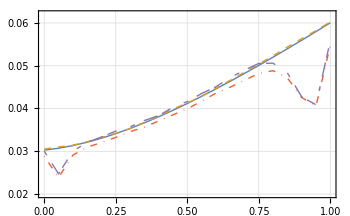
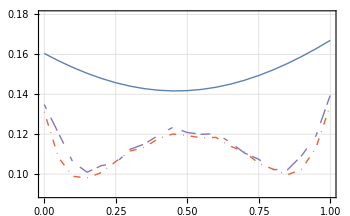
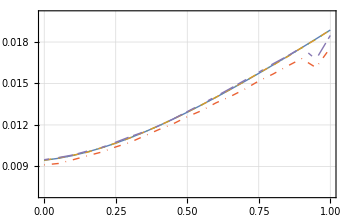
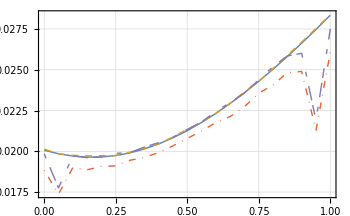
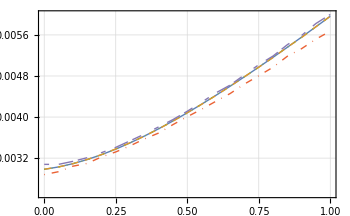
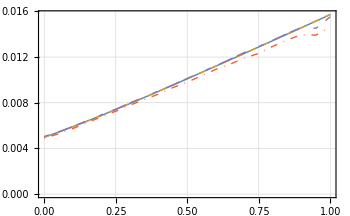
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- |

```mathematica
Grid[{{
exportme["risk-ld"]@PlotRisk["ld",None,PlotRange->{0.02,0.062}],
exportme["risk-md"]@PlotRisk["md",None,PlotRange->{0.007,0.02}],
exportme["risk-hd"]@PlotRisk["hd",None,PlotRange->{0.0025,0.006}]
},{
exportme["risk-lc"]@PlotRisk["lc",None,PlotRange->{0.09,0.18}],
exportme["risk-mc"]@PlotRisk["mc",None],
exportme["risk-hc"]@PlotRisk["hc",None]
},{
exportme["risk-legend"]@(First@Last@PlotRisk["ld",{0.2,0.65}]),Null,Null
}}ᵀ]
```